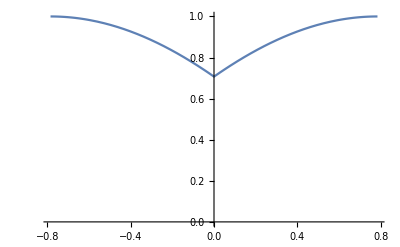

```mathematica
Plot[Cos[π/4-Abs@x],{x,-π/4,π/4},PlotRange->{0,1}]
```

```mathematica
Graphics3D[Point@ExampleData[{"Geometry3D","SpaceShuttle"},"VertexData"]]
```

```mathematica
cow=ExampleData[{"Geometry3D","SpaceShuttle"},"GraphicsComplex"]
```

```mathematica
Projection
```

```mathematica
FullForm[cow]
```

```mathematica
MapIndexed[Export["/Users/emileokada/Documents/Summer/space"<>ToString[#2[[1]]]<>".jpg",#1]&,Binarize[ColorConvert[#,"GrayScale"],0.9999]&/@Table[Graphics3D[{EdgeForm[None],GeometricTransformation[GeometricTransformation[cow,RotationTransform[π/2,{0,1,0}]],RotationTransform[k Pi,{0,0,1}]]},ViewPoint->{0,Infinity,0},PlotRange->{{-5,5},{-5,5},{-10,10}}],{k,-1,1,0.1}]]
```

{/Users/emileokada/Documents/Summer/space1.jpg,/Users/emileokada/Documents/Summer/space2.jpg,/Users/emileokada/Documents/Summer/space3.jpg,/Users/emileokada/Documents/Summer/space4.jpg,/Users/emileokada/Documents/Summer/space5.jpg,/Users/emileokada/Documents/Summer/space6.jpg,/Users/emileokada/Documents/Summer/space7.jpg,/Users/emileokada/Documents/Summer/space8.jpg,/Users/emileokada/Documents/Summer/space9.jpg,/Users/emileokada/Documents/Summer/space10.jpg,/Users/emileokada/Documents/Summer/space11.jpg,/Users/emileokada/Documents/Summer/space12.jpg,/Users/emileokada/Documents/Summer/space13.jpg,/Users/emileokada/Documents/Summer/space14.jpg,/Users/emileokada/Documents/Summer/space15.jpg,/Users/emileokada/Documents/Summer/space16.jpg,/Users/emileokada/Documents/Summer/space17.jpg,/Users/emileokada/Documents/Summer/space18.jpg,/Users/emileokada/Documents/Summer/space19.jpg,/Users/emileokada/Documents/Summer/space20.jpg,/Users/emileokada/Documents/Summer/space21.jpg}

```mathematica
Directory[]
```

/Users/emileokada